## Calculations for confidence-bound (Problem 12.5)

```mathematica
Clear["Global`*"];
```

```mathematica
eq=p==((1-b)((1-a)p+a(1-p)))/((1-b)((1-a)p+a(1-p))+b((1-a)(1-p)+a p));
sol=Solve[eq,p]//FullSimplify
```

{{p→(1-√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b+a (-3+4 b))/(2 (-1+2 a) (-1+2 b))},{p→(1+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b+a (-3+4 b))/(2 (-1+2 a) (-1+2 b))}}

```mathematica
eq1=Collect[p ((1-b)((1-a)p+a(1-p))+b((1-a)(1-p)+a p))-(1-b)((1-a)p+a(1-p)),p,Simplify]
```

a (-1+b)+(-1+a (3-4 b)+2 b) p+(-1+2 a) (-1+2 b) p^2

```mathematica
eq2=Collect[p((1−b)(a+p−2a p)+b(1−a−p+2a p))-(1−b)(a+p−2a p),p,Simplify]
```

a (-1+b)+(-1+a (3-4 b)+2 b) p+(-1+2 a) (-1+2 b) p^2

```mathematica
psol=p/.sol[[2]];
```

```mathematica
eq/.a->1/2//FullSimplify
```

b+p==1

```mathematica
sol1=Solve[b+p==1,p]
```

{{p→1-b}}

```mathematica
psol
```

(1+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b+a (-3+4 b))/(2 (-1+2 a) (-1+2 b))

```mathematica
p1=Plot[psol/.a->0.2,{b,0,0.5}];
psol/.{a->0.2,b->0.3}
```

0.851629

```mathematica
psol00=Series[psol,{b,0,1}];psol00n=FullSimplify[Normal[psol00],0<a<1/2]
```

1+(a b)/(-1+a)

```mathematica
psol05=Series[psol,{b,1/2,2}];psol05n=FullSimplify[Normal[psol05],a>0]
```

(1+2 a-2 b)/(4 a)

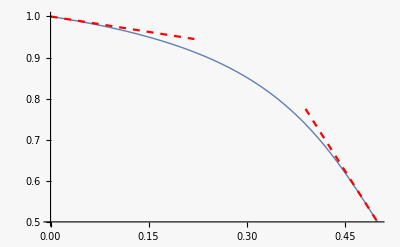

```mathematica
p2=Plot[psol00n/.a->0.2,{b,0,0.22},PlotStyle->{Red,Dashed}];
p3=Plot[psol05n/.a->0.2,{b,0.39,0.5},PlotStyle->{Red,Dashed}];
Show[p1,p2,p3]
```

Condition where filter inference first disagrees with observation:

```mathematica
(* eq3=(b((1-a)psol+a(1-psol)))/(b((1-a)psol+a(1-psol))+(1-b)(a psol+(1-a)(1-psol)))//FullSimplify *)
eq3=(b(a+psol−2a psol))/(b(a+psol−2a psol)+(1-b)(1−a−psol+2a psol))//FullSimplify
```

((1-a+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b) b)/((-1-a+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)) (-1+2 b))

```mathematica
t0=2b(1-a+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b)-(-1-a+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)) (-1+2 b)//Simplify
```

-1-a+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)+4 b-4 b^2

```mathematica
t1=a^2+(1-2 b)^2-2 a (1-2 b)^2==(4 b-4 b^2-1-a)^2//Simplify
```

(-1+2 b) (a+(-1+b) b)==0

```mathematica
sol3=Solve[eq3==1/2,b]
```

{{b→1/2 (1-√(1-4 a))},{b→1/2 (1+√(1-4 a))}}

```mathematica
{bsol3=b/.sol3[[1]],bsol3/.a->0.2}
```

{1/2 (1-√(1-4 a)),0.276393}

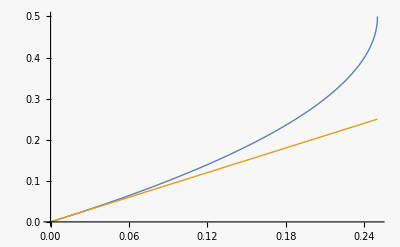

```mathematica
Plot[{bsol3,a},{a,0,0.25}]
```

Now repeat calculations using smoother estimate.  
Max. confidence condition is q =P(x_k=1 | y^N=1) for N large enough to have a fixed point.

```mathematica
eq4=q==p(((1-a)q)/(a+p-2a p)+(a(1-q))/(1-a-p+2a p));
sol4=Solve[eq4,q]//Simplify
```

{{q→(p (-p+a (-1+2 p)))/(-1+a (1-2 p)^2+2 p-2 p^2)}}

```mathematica
qsol=q/.sol4[[1]]//FullSimplify
```

(p (-p+a (-1+2 p)))/(-1+a (1-2 p)^2-2 (-1+p) p)

```mathematica
qsol1=qsol/.p->psol//FullSimplify
```

(1+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b+a (-1+2 b))/(2 √(a^2+(1-2 b)^2-2 a (1-2 b)^2))

```mathematica
qsol1a=1/2(1+((1-a)(1-2b))/(√(a^2+(1-2 b)^2-2 a (1-2 b)^2)));
```

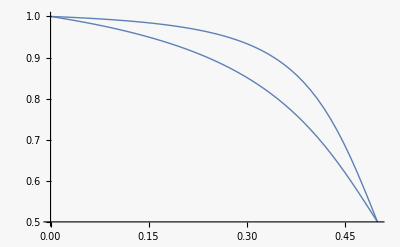

```mathematica
Plot[{psol,qsol1a}/.a->0.2,{b,0,0.5}]
```

```mathematica
{psol,qsol/.p->psol}/.{a->0.2,b->0.3} (* increase in confidence in particular case *)
```

{0.851629,0.933861}

```mathematica
Series[qsol1a,{a,0,2}]//FullSimplify
```

1/2 (1+(1-2 b)/(√((1-2 b)^2)))-((-1+b) b √((-1+2 b)^2) a^2)/(-1+2 b)^3+O[a]^3

For the phase transition threshold using the smoother, we use time symmetry...

```mathematica
eq5=(b(a+psol−2a psol)^2/((a+psol−2a psol)^2+(1−a−psol+2a psol)^2))/(b(a+psol−2a psol)^2/((a+psol−2a psol)^2+(1−a−psol+2a psol)^2)+(1-b)(1−a−psol+2a psol)^2/((a+psol−2a psol)^2+(1−a−psol+2a psol)^2))//FullSimplify
```

-((1-a+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-2 b)^2 b)/(2 (-a^2+a √(a^2+(1-2 b)^2-2 a (1-2 b)^2)+(-1+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)) (1-2 b)^2))

```mathematica
sol5=Solve[eq5==1/2,b]//FullSimplify
```

{{b→1/2},{b→1/2-(√(-(-1+a)^2 (1+a) (-1+3 a)))/(2 (-1+a)^2)},{b→1/2 (1+(√(-(-1+a)^2 (1+a) (-1+3 a)))/(-1+a)^2)}}

```mathematica
{bsol5=b/.sol5[[2]],bsol5/.a->0.2}
```

{1/2-(√(-(-1+a)^2 (1+a) (-1+3 a)))/(2 (-1+a)^2),0.0669873}

```mathematica
eq5a=2b(a+p−2a p)^2==b(a+p−2a p)^2+(1-b)(1−a−p+2a p)^2//FullSimplify
```

(-1+b) (-1+a+p-2 a p)^2+b (a+p-2 a p)^2==0

```mathematica
eq5b=eq5a/.p->psol//FullSimplify
```

1/(-1+2 b)(-1-a^2+√(a^2+(1-2 b)^2-2 a (1-2 b)^2)-4 (-1+b) b+a (√(a^2+(1-2 b)^2-2 a (1-2 b)^2)+4 (-1+b) b))==0

```mathematica
Solve[eq5b,b]//FullSimplify
```

{{b→1/2-(√(-(-1+a)^2 (1+a) (-1+3 a)))/(2 (-1+a)^2)},{b→1/2 (1+(√(-(-1+a)^2 (1+a) (-1+3 a)))/(-1+a)^2)}}

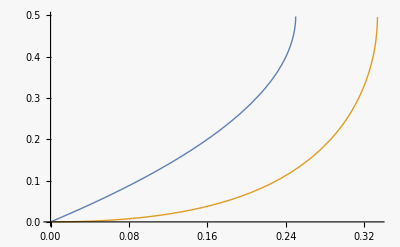

```mathematica
Plot[{bsol3,bsol5},{a,0,0.5}]
```

Output Latex forms to copy/paste into book manuscript

```mathematica
TeXForm[a (-1+b)+(-1+a (3-4 b)+2 b) p+(-1+2 a) (-1+2 b) p^2]
```

(2 a-1) (2 b-1) p^2+p (a (3-4 b)+2 b-1)+a (b-1)

```mathematica
TeXForm[sol[[2]]]
```

\left\{p\to \frac{\sqrt{a^2-2 a (1-2 b)^2+(1-2 b)^2}+a (4 b-3)-2 b+1}{2 (2 a-1) (2
   b-1)}\right\}